```mathematica
E2[n_,k_, b_]:= E2[n,k,b]=Sum[ E2[n/j,k-1,b],{j,2,n}]-b Sum[ E2[n/(b j),k-1,b],{j,1,n/b}];E2[n_,0,a_]:=1
D1[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
D11[n_, b_] := Sum[ b^j (E2[n/b^j,1,b]+ E2[n/b^j,0,b]),{j,0,Log[b,n]}]
E3[n_,b_]:= Sum[1,{j,2,n}]-b Sum[ 1,{j,1,n/b}]
D12[n_, b_] := Sum[ b^j (E3[n/b^j,b]+ 1),{j,0,Log[b,n]}]
D13[n_, b_] := Sum[ b^j (Sum[1,{j,2,n/b^j}]-b Sum[ 1,{j,1,n/b^(j+1)}]+ 1),{j,0,Log[b,n]}]
D14[n_, b_] := Sum[ b^j (Sum[1,{j,2,Floor[n/b^j]}]-b Sum[ 1,{j,1,Floor[n/b^(j+1)]}]+ 1),{j,0,Log[b,n]}]
D15[n_, b_] := Sum[ b^j (-b Floor[b^(-1-j) n]+Floor[b^-j n]),{j,0,Log[b,n]}]

D15[6,1.01]
```

6.

```mathematica
Log[1.01,6/1]
```

180.07

DiscretePlot::iterb: Iterator {j, 0, Log[b, n]} does not have appropriate bounds.

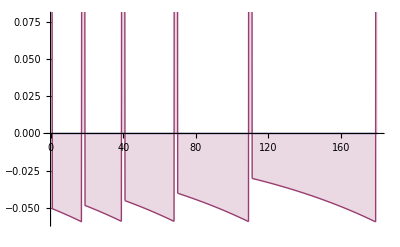

```mathematica
DiscretePlot[ {0,b^j (-b Floor[b^(-1-j) n]+Floor[b^-j n])},{j,0,Log[b,n]}]/.{b->1.01,n->6}
```

```mathematica
FullSimplify[Expand[b^j (Sum[1,{j,2,Floor[n/b^j]}]-b Sum[ 1,{j,1,Floor[n/b^(j+1)]}]+ 1)]]
```

b^j (-b Floor[b^(-1-j) n]+Floor[b^-j n])

```mathematica
Limit[Sum[ b^j (-b Floor[b^(-1-j) 6]+Floor[b^-j 6]),{j,0,Log[b,6]}],b->1]
```

$Aborted

```mathematica
Limit[Sum[ b^j (-b Floor[b^(-1-j) 6]+Floor[b^-j 6]),{j,1,Log[b,6/5]}],b->1]
```

$Aborted

```mathematica
Limit[Sum[ b^j (-b 5+5),{j,Log[b,6/6],Log[b,6/5]}],b->1]
```

-1

```mathematica
Limit[Sum[ b^j (-b 4+4),{j,Log[b,6/5],Log[b,6/4]}],b->1]
```

-6/5

```mathematica
Limit[Sum[ b^j (-b 3 +3),{j,Log[b,6/4],Log[b,6/3]}],b->1]
```

-3/2

```mathematica
Limit[Sum[ b^j (-b 2 +2),{j,Log[b,6/3],Log[b,6/2]}],b->1]
```

-2

```mathematica
Limit[Sum[ b^j (-b 1 +1),{j,Log[b,6/2],Log[b,6/1]}],b->1]
```

-3

```mathematica
-1 - 6/5 - 3/2 - 2 - 3
```

-87/10

```mathematica
(6/6+6/5+6/4 + 6/3+6/2+6/1)+(-1 - 6/5 - 3/2 - 2 - 3)
```

6

```mathematica
D21[n_, b_] := Sum[ (j+1) b^j 
Sum[FactorialPower[2,a]/a! E2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
D22[n_, b_] := Sum[ (j+1) b^j 
( E2[n/b^j,2,b]+2E2[n/b^j,1,b]+E2[n/b^j,0,b]),{j,0,Log[b,n]}]
D23[n_, b_] := Sum[ (j+1) b^j 
( E2[n/b^j,2,b]+2(Sum[1,{r,2,Floor[n/b^j]}]-b Sum[ 1,{r,1,Floor[n/b^(j+1)]}])+1),{j,0,Log[b,n]}]
D25[n_, b_] := Sum[ (j+1) b^j 
( (Sum[1,{r,2,n/b^j},{k,2,Floor[n/r/b^j]}]-2b Sum[ 1,{r,1,Floor[n/b/b^j]},{k,2,Floor[n/(r b)/b^j]}]+b^2 Sum[ 1,{r,1,Floor[n/b/b^j]}, {k,1,Floor[n/(b^2 r)/b^j]}])+2(Sum[1,{r,2,Floor[n/b^j]}]-b Sum[ 1,{r,1,Floor[n/b^(j+1)]}])+1),{j,0,Log[b,n]}]
D26[n_, b_] := Sum[ (j+1) b^j 
( (Sum[1,{r,2,n/b^j},{k,2,Floor[n/r/b^j]}]-2b Sum[ 1,{r,1,Floor[n/b/b^j]},{k,2,Floor[n/(r b)/b^j]}]+b^2 Sum[ 1,{r,1,Floor[n/b/b^j]}, {k,1,Floor[n/(b^2 r)/b^j]}])+2(Sum[1,{r,2,Floor[n/b^j]}]-b Sum[ 1,{r,1,Floor[n/b^(j+1)]}])+1),{j,0,Log[b,n]}]
D27[n_, b_] := Sum[ (j+1) b^j 
( (Sum[1,{r,2,n/b^j},{k,2,Floor[n/r/b^j]}]-2b Sum[ 1,{r,1,Floor[n/b/b^j]},{k,2,Floor[n/(r b)/b^j]}]+b^2 Sum[ 1,{r,1,Floor[n/b/b^j]}, {k,1,Floor[n/(b^2 r)/b^j]}])+2(Floor[n/b^j]-1-b Floor[n/b^(j+1)])+1),{j,0,Log[b,n]}]
```

```mathematica
D27[100,2]
```

482

```mathematica
Binomial[1+j,1]
```

1+j

```mathematica
E3a[n_,b_]:= Sum[1,{r,2,n},{k,2,Floor[n/r]}]-2b Sum[ 1,{r,1,Floor[n/b]},{k,2,Floor[n/(r b)]}]+b^2 Sum[ 1,{r,1,Floor[n/b]}, {k,1,Floor[n/(b^2 r)]}]
```

```mathematica
E3a[1200,3]
```

-20

```mathematica
E2[1200,2,3]
```

-20

```mathematica
FullSimplify[(j+1) b^j 
( (Sum[1,{r,2,n/b^j},{k,2,Floor[n/r/b^j]}]-2b Sum[ 1,{r,1,Floor[n/b/b^j]},{k,2,Floor[n/(r b)/b^j]}]+b^2 Sum[ 1,{r,1,Floor[n/b/b^j]}, {k,1,Floor[n/(b^2 r)/b^j]}])+2(Sum[1,{r,2,Floor[n/b^j]}]-b Sum[ 1,{r,1,Floor[n/b^(j+1)]}])+1)]
```

```mathematica
Expand[b^j (1+j) (-1+2 Floor[b^-j n]+b (-2 Floor[b^(-1-j) n]+b ∑_(r=1)^Floor[b^(-1-j) n] ∑_(k=1)^Floor[(b^(-2-j) n)/r] 1-2 ∑_(r=1)^Floor[b^(-1-j) n] ∑_(k=2)^Floor[(b^(-1-j) n)/r] 1)+∑_(r=2)^(b^-j n) ∑_(k=2)^Floor[(b^-j n)/r] 1)]
```

-b^j-b^j j-2 b^(1+j) Floor[b^(-1-j) n]-2 b^(1+j) j Floor[b^(-1-j) n]+2 b^j Floor[b^-j n]+2 b^j j Floor[b^-j n]+b^(2+j) ∑_(r=1)^Floor[b^(-1-j) n] ∑_(k=1)^Floor[(b^(-2-j) n)/r] 1+b^(2+j) j ∑_(r=1)^Floor[b^(-1-j) n] ∑_(k=1)^Floor[(b^(-2-j) n)/r] 1-2 b^(1+j) ∑_(r=1)^Floor[b^(-1-j) n] ∑_(k=2)^Floor[(b^(-1-j) n)/r] 1-2 b^(1+j) j ∑_(r=1)^Floor[b^(-1-j) n] ∑_(k=2)^Floor[(b^(-1-j) n)/r] 1+b^j ∑_(r=2)^(b^-j n) ∑_(k=2)^Floor[(b^-j n)/r] 1+b^j j ∑_(r=2)^(b^-j n) ∑_(k=2)^Floor[(b^-j n)/r] 1